```mathematica
CloseKernels[];
LaunchKernels[8];
<<SpinWeightedSpheroidalHarmonics`
<<KerrGeodesics`
<<GeneralRelativityTensors`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"]
ParallelNeeds["KerrGeodesics`"]
ParallelNeeds["GeneralRelativityTensors`"]
ParallelNeeds["Teukolsky`"]
prec=40;
```

```mathematica
αstring=Import["C:\\Users\\SMP22EJG\\Documents\\GitHub\\ConservativeSelfForce\\Notebooks\\TPPM\\TPPMStringTable..a0..p20..e0.3..regionI..LMAX30..NMAX10.dat"];
αs =Uncompress[αstring[[1,1]]];
α[s_,l_,m_,n_]:=Uncompress[αs[[If[s==-1,1,2], l,m +l+1,n+11]]];
```

```mathematica
α[1,31,0,0]
```

Part::partw: Part 31 of {{{1:eJztmNuPHEcVxs1FQQkkXCTggRd4QEhI26o6derGNbYxIiJLzKytvCC0w0yv3fJcVnOJbPgneeLP4JFX+J<<2672>>FsrsQiIDPWnXwlHeyAdsKIhcJUQ8swEOPl/wAHE6h+, <<20>>}, <<2>>}, <<29>>} does not exist.

Uncompress::string: String expected at position 1 in Uncompress[{{{{1:eJztmduPHEcVxk1AQQkkXISSB17gASEhuVWnTl0RD7GNERFZsszaygtCO5np<<2777>>He1/0bwzcxh+Oh3ljD4UqON+G/Wgd2X, <<20>>}, <<2>>}, <<29>>}, {<<30>>}}[[2,<<2>>,11]]].

```mathematica
αs
```

```mathematica
𝔰[sp_,l_,lp_, m_]:= -sp  Sqrt[(2(2l+1))/(2 lp +1)]ClebschGordan[{l,m},{1,0},{lp,m}] ClebschGordan[{l,-sp} ,{1,sp }, {lp ,0}]
Ccoef[s_,j_,k_,m_,bs_]:=𝔰[s,j,k,m]*(j/.bs);
CLcoef [a_,m_,n_,j_,k_,ω_, bs_]:=(j/.bs)*(Sqrt[j(j+1)] KroneckerDelta[j,k] - a ω 𝔰[+1, j,k,m]);
```

```mathematica
Fr0[a_,τ_,  orbit_, k_,m_,n_, LMAX_]:= Module[{A,B,t, r,θ,φ,K0,Σ,Δ},
{t,r,θ,φ}=orbit["Trajectory"];
Δ=r[τ]^2-2 M r[τ] + a^2/.M->1;
Σ=r[τ]^2+ a^2 Cos[θ[τ]]^2;
K0= ω[m,n]((r[τ])^2 + a^2)- a m;

Sum[Module[{bsplus,bsminus,χ, g, dP,Β,Pminus, Pplus,Rminus, λ, cl, cp, cm, 𝒟P},
bsplus = SpinWeightedSpheroidalHarmonicS[1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX+1}]["ExpansionCoefficients"] ;
bsminus = SpinWeightedSpheroidalHarmonicS[-1,l,m,N[a ω[m,n]],Method->{"SphericalExpansion","NumTerms"->LMAX+1}]["ExpansionCoefficients"] ;
cl =CLcoef[a, m, n ,j,k,ω[m,n],bsplus];
cp = Ccoef[1, j, k, m , bsplus];
cm = Ccoef[-1, j,k,m, bsminus];

If[cl ==0&&cp==0&&cl==0,0,
λ = SpinWeightedSpheroidalEigenvalue[-1,l,m,a ω[m,n]];
Β= Sqrt[λ^2+ 4 a m ω[m,n] - 4 a^2 ω[m,n]^2];

Pminus= 2α[-1,l,m,n]["ExtendedHomogeneous"->"ℋ"][r[τ]];
Pplus = Δ α[+1,l,m,n]["ExtendedHomogeneous"->"ℋ"][r[τ]];
dP =2α[-1,l,m,n]["ExtendedHomogeneous"->"ℋ"]'[r[τ]] ;
𝒟P =dP - ⅈ K0/Δ Pminus; 
g= 1/Β (r[τ]𝒟P-Pminus);
χ=Exp[-ⅈ *ω[m,n]*t[τ] + ⅈ *m *φ[τ]];

A = Re[χ(cl g + ⅈ a cp/Β 𝒟P)];
B=- Im[χ(cm Pminus - cp*Pplus)];
tmp=(Sqrt[2] (t'[τ] - a φ'[τ]))/(r[τ]^2 Σ)A + (φ'[τ] *(a^2+r[τ]^2) + a t'[τ])/(Sqrt[2] Δ r[τ] Σ)B;
tmp
]
],{l,Max[1,Abs[m]],LMAX}, {j, k-1, k+1}]
]
```

```mathematica
N[1/Sqrt[2]]
```

0.707107

```mathematica
Off[ClebschGordan::tri ]
Off[ClebschGordan::phy]
ParallelEvaluate[Off[ClebschGordan::tri ]]
ParallelEvaluate[Off[ClebschGordan::phy]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
AbsoluteTiming[Module[{t,r,Ε,L,θ,φ, const,a=SetPrecision[0,prec], e=SetPrecision[0.3,prec],p=SetPrecision[20,prec],x=1, τ=0.5,LMAX= 30,NMax=10},
q=1;
orbit = KerrGeoOrbit[a,p,e,x]; 
{t,r,θ,φ}=orbit["Trajectory"];
Ω =KerrGeoFrequencies[a,p,e,x];
const=KerrGeoConstantsOfMotion[a,p,e,x];
Ε=const[[1]];
L = const[[2]];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
regParams[];
kmodes =ParallelTable[Sum[Fr0[a,τ,  orbit,k ,m,n, LMAX]SpinWeightedSphericalHarmonicY[0,k,m,θ[τ],0], {m,-k,k}, {n,-NMax, NMax}],{k,1,kmax}]
]]
```

NIntegrate::inumr: The integrand √(1-k Sin[β]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

NIntegrate::inumr: The integrand 1/(√(1-k Sin[β]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

-0.000972922

-0.000972922

0.00096186

0.0000760517

{3850.37,{0.00194282,0.00389897,0.00585504,0.00778611,0.00945866,0.0104103,0.00922653,0.00872559,0.0137197,0.0385325,0.0880692,0.149499,0.184701,0.158403}}

```mathematica
data1 = Table[{Log[i],Log[Abs[-kmodes[[i]]]]},{i,1,6}];
fit1 = Fit[data1, {1,y},y]
data2 = Table[{Log[i],Log[Abs[-kmodes[[i]]-(2i+1)reg1S]]},{i,1,5}];
fit2 = Fit[data2, {1,y},y]
data3 = Table[{Log[i],Log[Abs[-kmodes[[i]]-(2i+1)reg1S- reg0S]]},{i,1,4}];
fit3 = Fit[data3, {1,y},y]
data4 = Table[{Log[i],Log[Abs[-kmodes[[i]]-(2i+1)reg1S- reg0S-reg2S/((2i-1) (2i+3))]]},{i,1,2}];
fit4 = Fit[data4, {1,y},y]

data5 = Table[{Log[i],Log[Abs[-kmodes[[i]]-(2i+1)reg1S- reg0S-reg2S/((2i-1) (2i+3))-reg4S/((2i-3)(2i-1) (2i+3)(2i+5))]]},{i,1,2}];
fit5 = Fit[data5, {1,y},y]
```

-6.21875+0.957584 y

-6.98321+0.0960789 y

-11.5221-0.382838 y

-13.6961-2.86769 y

-12.0467-2.36258 y

```mathematica
kmax = 14
```

14

```mathematica
fit
```

-6.16949+0.988666 y

```mathematica
regParams[]:=
Module[{t,r,Ε,L,θ,φ, const,a=SetPrecision[0,prec], e=SetPrecision[0.3,prec],p=SetPrecision[20,prec],x=1, τ=0.5,LMAX= 40,NMax=0},
q=1;
orbit = KerrGeoOrbit[a,p,e,x]; 
{t,r,θ,φ}=orbit["Trajectory"];
Ω =KerrGeoFrequencies[a,p,e,x];
const=KerrGeoConstantsOfMotion[a,p,e,x];
Ε=const[[1]];
L = const[[2]];
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
(*-1 for Horizon 1 for Infinity*)
reg1 =-1((Ε r[τ](a^2 + r[τ]^2) + 2 a M (a Ε - L))/(2(a^2-2 M r[τ] + r[τ]^2) (r[τ](a^2 + L^2)+ 2 a^2 M + r[τ]^3)))/.M->1; 
reg1S = -(Ε r[τ])/(2 (r[τ] - 2M)(L^2+r[τ]^2))/.M->1;
Fr0ℰS = 2 Ε^2 L^2 r[τ]^3+(L^2+r[τ]^2)(2 L^2+ r[τ]^2)(2M - r[τ])/.M->1;
Fr0𝒦S = Ε^2 r[τ]^5+ r[τ]^2(L^2+r[τ]^2)(r[τ]-2M)/.M->1;

(*ask why we use this k ... this value was just copied from the scalar case code*)
ℰ = NIntegrate[(1-k Sin[β]^2)^(1/2),{β,0,π/2}]/.k->L^2/(r[τ]^2+L^2);
𝒦 = NIntegrate[(1-k Sin[β]^2)^(-1/2),{β,0,π/2}]/.k->L^2/(r[τ]^2+L^2);

reg0S = 1/(π r[τ]^3 (r[τ]^2+L^2)^(3/2)(r[τ]-2M))(Fr0ℰS ℰ+ 𝒦 Fr0𝒦S)/.M->1;
Frℰ2S= -2 Ε^4 r[τ]^8(-L^4+10 L^2 r[τ]^2+ 3 r[τ]^4)-(L^2+r[τ]^2)^2(2M-r[τ])(44 L^6 M +94 L^4 M r[τ]^2 +54 L^2 M r[τ]^4+L^2 r[τ]^5+3 r[τ]^7) + 2 Ε^2 r[τ]^3(L^2+r[τ]^2)(-30 L^6 M -86 L^4 M r[τ]^2+ L^4 r[τ]^3-98 L^2 M r[τ]^4 + 10 L^2 r[τ]^5-26 M r[τ]^6+r[τ]^7);
Fr𝒦2S= Ε^4 r[τ]^10(11 L^2+3 r[τ]^2)-r[τ]^2(L^2+r[τ]^2)^2(r[τ]-2M)(22 L^4 M + 24 L^2 M r[τ]^2+2 L^2 r[τ]^3 + 3 r[τ]^5)+Ε^2 r[τ]^5(L^2+r[τ]^2)(42 L^4 M+98 L^2 M r[τ]^2-7 L^2 r[τ]^3+40 M r[τ]^4+r[τ]^5);
reg2S = -1/(2π r[τ]^6(L^2+r[τ]^2)^(7/2)(r[τ] -2M))*(Frℰ2S ℰ+ Fr𝒦2S 𝒦)/.M->1;

Frℰ4S =30 Ε^6 r[τ]^17(3 L^6-102 L^4 r[τ]^2+43 L^2 r[τ]^4+20 r[τ]^6)-Ε^4 r[τ]^8(L^2+r[τ]^2)(69120 L^12 M +339456 L^10 M r[τ]^2+667128 L^8 M r[τ]^4+657884 L^6 M r[τ]^6-30 L^6 r[τ]^7 +334658 L^4 M r[τ]^8 - 2745 L^4 r[τ]^9+62656 L^2 M r[τ]^10+4080 L^2 r[τ]^11 + 610M r[τ]^12 + 1035 r[τ]^13) +(L^2+r[τ]^2)^3 (2M-r[τ])( 46080 L^14 M^2 + 89856 L^12 M^2 r[τ]^2+53760 L^12 M r[τ]^3-86336 L^10 M^2 r[τ]^4+211520 L^10 M r[τ]^5-344128 L^8 M^2 r[τ]^6+317600 L^8 M r[τ]^7-306808 L^6 M^2 r[τ]^8+221140 L^6 M r[τ]^9-98676 L^4 M^2 r[τ]^10+66220 L^4 M r[τ]^11+60 L^4 r[τ]^12-5244 L^2 M^2 r[τ]^12+4440 L^2 M r[τ]^13+105 L^2 r[τ]^14+160 M^2 r[τ]^14-75 r[τ]^16)+2 Ε^2 r[τ]^3(L^2+r[τ]^2)^2(23040 L^14 M^2 - 36480 L^12 M^2 r[τ]^2+67200 L^12 M r[τ]^3-445056 L^10 M^2 r[τ]^4+303824 L^10 M r[τ]^5-959952 L^8 M^2 r[τ]^6+545340 L^8 M r[τ]^7-922996 L^6 M^2 r[τ]^8+486240 L^6 M r[τ]^9-428644 L^4 M^2 r[τ]^10+216604 L^4 M r[τ]^11+105 L^4 r[τ]^12-78428 L^2 M^2 r[τ]^12+35368 L^2 M r[τ]^13+1350 L^2 r[τ]^14-2684 M^2 r[τ]^14+608 M r[τ]^15+165 r[τ]^16);

Fr𝒦4S = -15 Ε^6 r[τ]^19(-87 L^4+66 L^2 r[τ]^2+25 r[τ]^4)+Ε^4 r[τ]^10(L^2+r[τ]^2)(34560 L^10 M+139488 L^8 M r[τ]^2+213132 L^6 M r[τ]^4+150250 L^4 M r[τ]^6-915 L^4 r[τ]^7+37496 L^2 M r[τ]^8+2550 L^2 r[τ]^9+1210 M r[τ]^10+585 r[τ]^11)-r[τ]^2(L^2+r[τ]^2)^3(r[τ]-2M)(63760 L^8 M^2 r[τ]^4-23040 L^12 M^2-24768 L^10 M^2 r[τ]^2-26880 L^10 M r[τ]^3-82240 L^8 M r[τ]^5+115848 L^6 M^2 r[τ]^6-87920 L^6 M r[τ]^7+56084 L^4 M^2 r[τ]^8-36340 L^4 M r[τ]^9+5324 L^2 M^2 r[τ]^10-3540 L^2 M r[τ]^11+15 L^2 r[τ]^12-160 M^2 r[τ]^12+75 r[τ]^14)-Ε^2 r[τ]^5(L^2+r[τ]^2)^2(23040 L^12 M^2-56640 L^10 M^2 r[τ]^2+67200 L^10 M r[τ]^3-394416 L^8 M^2 r[τ]^4+245024 L^8 M r[τ]^5-618528 L^6 M^2 r[τ]^6+334004 L^6 M r[τ]^7-400636 L^4 M^2 r[τ]^8+203252 L^4 M r[τ]^9+180 L^4 r[τ]^10-97892 L^2 M^2 r[τ]^10+44568 L^2 M r[τ]^11+1365 L^2 r[τ]^12-5368 M^2 r[τ]^12+1816 r[τ]^13+105 r[τ]^14);

reg4S = 3/(40π r[τ]^13(L^2+r[τ]^2)^(11/2)(r[τ]-2M))(Frℰ4S ℰ + Fr𝒦4S 𝒦)/.M->1;

Print[reg1S];
Print[reg1];
Print[reg0S];
Print[reg2S];
Print[reg4S];
];
regParams[]
```

NIntegrate::inumr: The integrand √(1-k Sin[β]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

NIntegrate::inumr: The integrand 1/(√(1-k Sin[β]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.5708}}.

-0.000972922

-0.000972922

0.00096186

0.0000760517

0.000244678

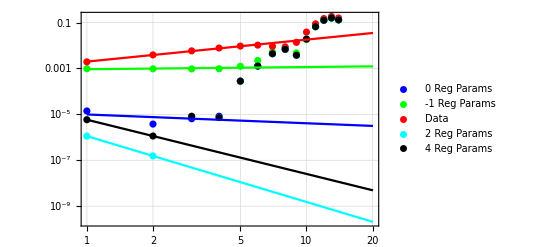

```mathematica
Show[ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]-(2l+1)reg1S- reg0S]},{l,1,kmax}], PlotStyle->Blue,PlotLegends->{"0 Reg Params"}],
ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]-(2l+1)reg1S] },{l,1,kmax}], PlotStyle->Green,PlotLegends->{"-1 Reg Params"}],ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]]},{l,1,kmax}], PlotStyle->Red,PlotLegends->{"Data"}],ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]-(2l+1)reg1S- reg0S-reg2S/((2l-1) (2l+3))]},{l,1,kmax}], PlotStyle->Cyan,PlotLegends->{"2 Reg Params"}],ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]-(2l+1)reg1S- reg0S-reg2S/((2l-1) (2l+3))-reg4S/((2l-3)(2l-1) (2l+3)(2l+5))]},{l,1,kmax}], PlotStyle->Black,PlotLegends->{"4 Reg Params"}],Plot[fit1,{y,0,3},PlotStyle->Red],Plot[fit2,{y,0,3},PlotStyle->Green], Plot[fit3,{y,0,3},PlotStyle->Blue],Plot[fit4,{y,0,3},PlotStyle->Cyan],Plot[fit5,{y,0,3},PlotStyle->Black],GridLines->Automatic, PlotRange->Full, Frame->True]
```

```mathematica
kmodes
```

{0.00194282,0.00389897,0.00585504,0.00778611,0.00945866,0.0104103,0.00922653,0.00872559,0.0137197,0.0385325,0.0880692,0.149499,0.184701,0.158403}

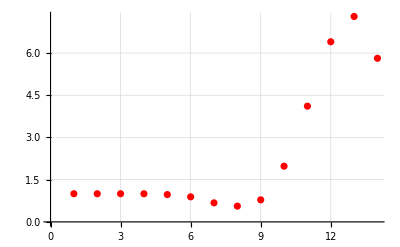

```mathematica
ListPlot[Table[{l,kmodes[[l]]/(-(2l+1)reg1S-reg0S-reg2S/((2l-1) (2l+3)))},{l,1,kmax}], PlotStyle->Red,GridLines->Automatic]
```

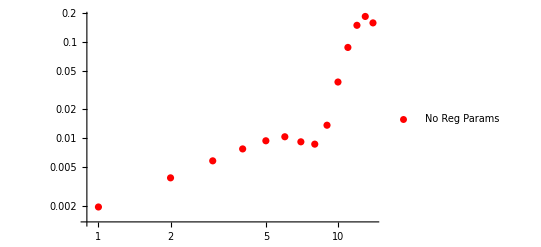

```mathematica
ListLogLogPlot[Table[{l,Abs[-kmodes[[l]]]},{l,1,kmax}], PlotStyle->Red,PlotLegends->{"No Reg Params"}]
```